# PerturbedArrayPlot

Plot an array with arrows drawn to the specified perturbed cells

## Definition

```mathematica
Options[PerturbedArrayPlot] = {"ArrowStyle"->Directive[Red, Arrowheads[.075]],"ArrowDirection"->Automatic, "InitialIndex"->1};
```

```mathematica
(* Single arrow *) 
PerturbedArrayPlot[array: {{_?NumericQ..}..}, {i_Integer, j_Integer}, ops: OptionsPattern[{PerturbedArrayPlot, ArrayPlot}]]:=
Module[{allops  =Merge[{Options[PerturbedArrayPlot],ops},Last]},
ArrayPlot[array,FilterRules[Normal[allops], Options[ArrayPlot]], Mesh->True, Epilog->({Red, Arrowheads[.075],allops["ArrowStyle"], With[{start = If[allops["ArrowDirection"] === Automatic, If[j<=Ceiling[(Length[array[[1]]])/2], 0, Length[array[[i]]]],If[allops["ArrowDirection"] === "Right", 0,Length[array[[1]]]]]}, Arrow[{{start, Length[array] - i + .5  + (allops["InitialIndex"] - 1)},{j-.5 ,Length[array] - i +.5  + (allops["InitialIndex"] - 1)}}]]})]]
```

```mathematica
(* Multiple arrows *) 
PerturbedArrayPlot[array:{{_?NumericQ..}..}, reps: {{_Integer, _Integer}...}, ops:OptionsPattern[{PerturbedArrayPlot, ArrayPlot}]]:=
Module[{allops  =Merge[{Options[PerturbedArrayPlot],ops},Last]},
ArrayPlot[array,FilterRules[Normal[allops], Options[ArrayPlot]],Mesh->True, Epilog->({Red, Arrowheads[.075],
Function[{i, j, style, direction},
With[{start = 
If[direction === Automatic,
If[j<=Ceiling[(Length[array[[1]]])/2], 0, Length[array[[i]]]],If[direction === "Right", 0, Length[array[[i]]]]]}, 
Style[
Arrow[{{start, Length[array] - i + .5  + (allops["InitialIndex"] - 1)},{j-.5 ,Length[array] - i +.5 + (allops["InitialIndex"] - 1)}}], style]
]]@@@
MapThread[
Join[#1, {#2, #3}]&, {reps, If[ListQ[allops["ArrowStyle"]], allops["ArrowStyle"], Table[allops["ArrowStyle"], Length[reps]]],
If[ListQ[allops["ArrowDirection"]], allops["ArrowDirection"], Table[allops["ArrowDirection"], Length[reps]]]
}]})]]
```

## Documentation

### Usage

PerturbedArrayPlot[array,{i,j}]

plots array with an arrow drawn to {i,j}.

PerturbedArrayPlot[array,{{i_1,j_1},…}]

plots array with arrows drawn to {i_n, j_n}.

### Details & Options

In addition to all the options for ArrayPlot PerturbedArrayPlot takes the following options

"ArrowStyle" | Directive[Red, Arrowheads[.075]] | directive to style the arrow
"ArrowDirection" | Automatic | which direction the arrow points
“InitialIndex" | 1 | the initial index touse for the index specification

## Examples

### Basic Examples

Plot an array with an arrow drawn to the second cell of the second row:

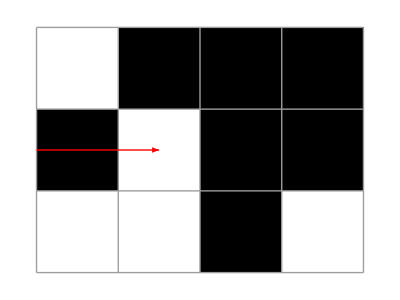

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {2, 2}]
```

Plot the same array with two cells indicated:

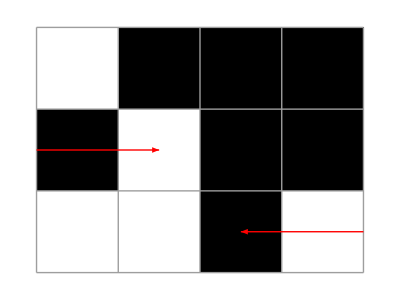

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1, 1},{0,0,1, 0}}, {{2, 2}, {3, 3}}]
```

### Scope

### Options

Change the color of the arrow:

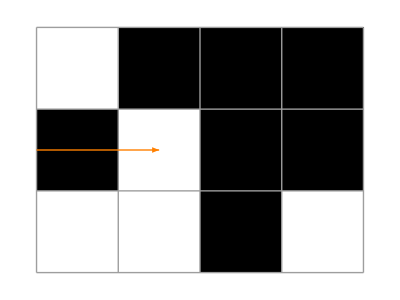

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {2, 2}, "ArrowStyle"->Orange]
```

Increase the size of the arrowhead:

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {2, 2}, "ArrowStyle"->Arrowheads[.2]]
```

-Graphics-

Increase the thickness of the stem of the arrow:

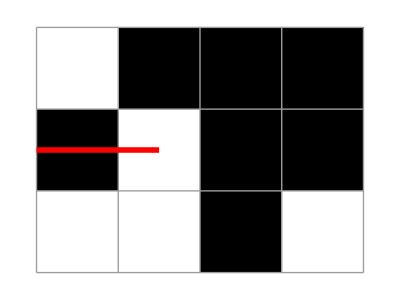

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {2, 2}, "ArrowStyle"->Thickness[.01]]
```

Use directive to apply multiple styles:

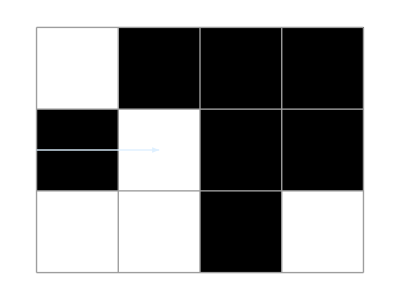

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {2, 2}, "ArrowStyle"->Directive[Haloing[Red], LightBlue]]
```

By default styles are applied to all arrows:

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {{2, 2}, {3, 3}}, "ArrowStyle"->Directive[Haloing[Red], LightBlue]]
```

-Graphics-

Use a list of style directives to specify different styling for each arrow:

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {{2, 2}, {3, 3}}, "ArrowStyle"->{Blue, Orange}]
```

-Graphics-

Specify the arrow direction:

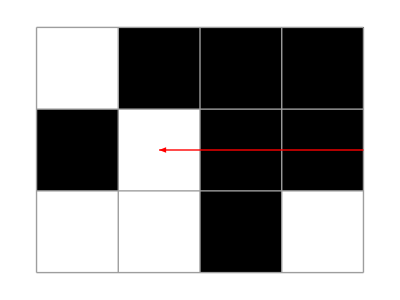

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {2, 2}, "ArrowDirection"->"Left"]
```

By default, arrow direction is applied to all arrows:

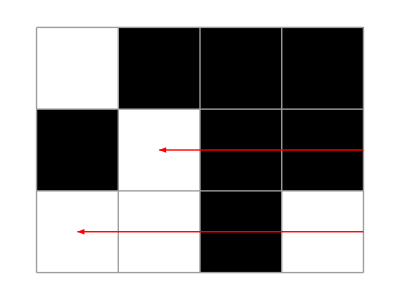

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {{2, 2}, {3, 1}}, "ArrowDirection"->"Left"]
```

Specify two different arrow directions:

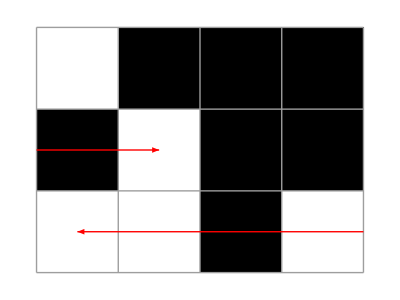

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {{2, 2}, {3, 1}}, "ArrowDirection"->{"Right", "Left"}]
```

Automatic makes the arrow start from the side that's further away from the perturbed cell:

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {{2, 2}, {3, 1}}, "ArrowDirection"->{Automatic, "Left"}]
```

-Graphics-

Use the "InitialIndex" option to start from an index of 0, which is useful when plotting cellular automata:

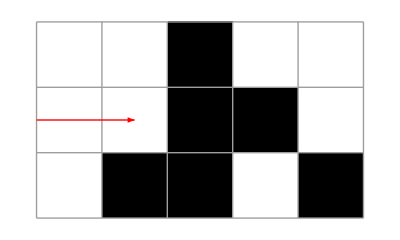

```mathematica
PerturbedArrayPlot[#1, Keys[#2], "InitialIndex"->0]&@@[30,{{1},0},{2,{-2,2}},{1,2}->0]
```

### Applications

Observe the effect of perturbing rule 30:

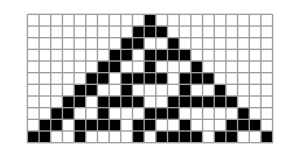
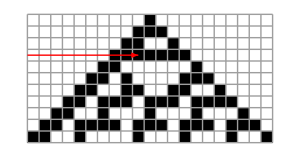

```mathematica
PerturbedArrayPlot[#1, Keys[#2], "InitialIndex"->0, "ArrowStyle"->Directive[Haloing[White], Thickness[.01]], ImageSize->300,"ArrowDirection"->"Right"]&@@@{{CellularAutomaton[30, {{1}, 0},{10, {-10, 10}}] , {}},[30,{{1},0},{10, {-10, 10}},{{3,3}}->"Random", "Body"->True]}
```

See the effects of single perturbations on "adaptively evolved" automata:

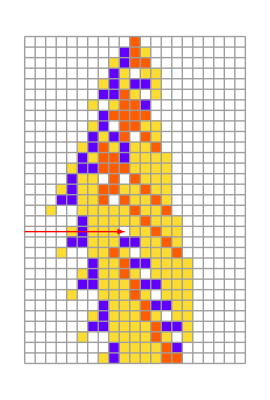

```mathematica
PerturbedArrayPlot[#1, Keys[#2], "InitialIndex"->0,"ArrowStyle"->Directive[GrayLevel[.3], Haloing[Lighter[Cyan, .8]]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&@@[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, {30, {-10, 10}}, {18, 10}->{"AddValue", 1}]
```

See the effects of multiple perturbations:

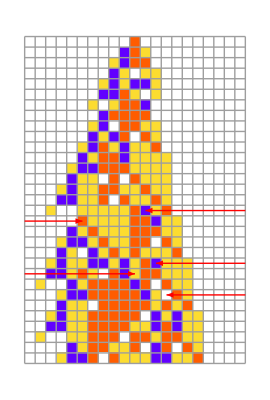

```mathematica
PerturbedArrayPlot[#1, Keys[#2], "InitialIndex"->0,"ArrowStyle"->Directive[GrayLevel[.3], Haloing[Lighter[Cyan, .8]]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&@@[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, {30, {-10, 10}},{RandomSample[#[[15;;25]], 5]&, RandomChoice}, "Body"->True]
```

Look at the effect of many different single perturbations on a different adaptively evolved automata:

```mathematica
GraphicsGrid[Partition[Table[PerturbedArrayPlot[#1, Keys[#2],"InitialIndex"->0,"ArrowStyle"->Directive[Arrowheads[.15],GrayLevel[.35], Haloing[Lighter[Cyan, .85]]], ImageSize->{Automatic,400}, Mesh->False, ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&@@With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{150,{-8,36}},1]],{i,30}],10]]
```

-Graphics-

Illustrate the progression of a constraint-satisfaction system from New Kind of Science:

```mathematica
ConstraintViolations[array_]:=Count[Partition[array,{3,3},1],{{_,a_,_},{b_,x_,c_},{_,d_,_}}/;!(a+b+c+d==If[x==1,1,2]),{2}];
```

```mathematica
SeedRandom[3060];
arrs = Gather[NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000]];
```

```mathematica
pos = SparseArray[#]["ExplicitPositions"]&/@ Subtract@@@Partition[arrs[[All, 1]], 2, 1];
```

```mathematica
reps = MapThread[ReplacePart[#1, Thread[#2->Red]]&, {arrs[[2;;,1]], pos}];
```

```mathematica
MapThread[PerturbedArrayPlot[#1, #2, "ArrowStyle"->Directive[Haloing[White],Arrowheads[.1]], ImageSize->120]&,{arrs[[2;;6, 1]],pos[[;;5]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Properties and Relations

If given an empty list it behaves the same as an empty list:

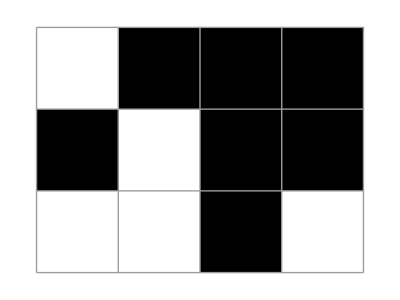

```mathematica
PerturbedArrayPlot[{{0,1,1, 1},{1,0,1,1},{0,0,1, 0}}, {}]
```

### Possible Issues

If you don't specify "InitialIndex" goes to 0, when using it with PerturbedCellularAutomata, the arrow will go to the wrong square:

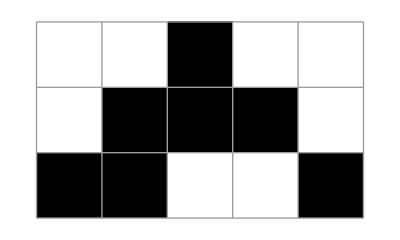
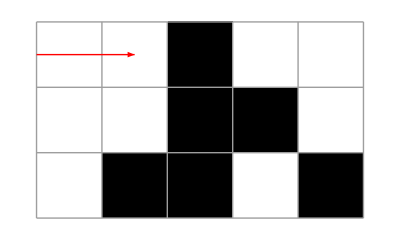

```mathematica
PerturbedArrayPlot[#1, Keys[#2]]&@@@{{CellularAutomaton[30,{{1},0},{2,{-2,2}}], <||>},[30,{{1},0},{2,{-2,2}},{1,2}->0]}
```

Corrected:

```mathematica
PerturbedArrayPlot[#1, Keys[#2], "InitialIndex"->0]&@@@{{CellularAutomaton[30,{{1},0},{2,{-2,2}}], <||>},[30,{{1},0},{2,{-2,2}},{1,2}->0]}
```

{-Graphics-,-Graphics-}

### Neat Examples

## Source & Additional Information

### Contributed By

Willem Nielsen

### Keywords

Cellular Automata

Adaptive Evolution

Perturbed Evolution

Behavior Under Uncertainty

Fragility

Robustness

Ruliology

Visualization

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

ArrayPlot

CellularAutomaton

### Related Resource Objects

PerturbedCellularAutomaton

### Source/Reference Citation

### Links

### Tests

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.